Página 31, Linealización de ese ejercicio

```mathematica
Datos1={{1/873.15,Log[1.87*10^(-3)]},{1/923.15,Log[0.0113]},{1/973.15,Log[0.0569]},{1/1023.15,Log[0.244]}}
```

{{0.00114528,-6.28182},{0.00108325,-4.48295},{0.00102759,-2.86646},{0.000977374,-1.41059}}

```mathematica
ml=LinearModelFit[Datos1,{1,x},x]
```

FittedModel[26.9483-29015.1 x]

```mathematica
R=8.314
Ea=-29015.073859744494*R
```

8.314

-241231.

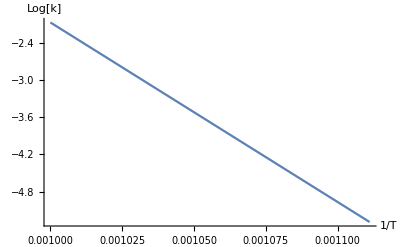

```mathematica
Plot[ml[x],{x,1/1000,1/900},AxesLabel->{"1/T","Log[k]"},Axes->{True,True}AxesOrigin->{1/900,-1.8}]
```